## (1) Given a height function, get the pressure distribution. Testing: The Hard Sphere Solution.

Nondimensionalised, the hard sphere problem is:

1/x d/dx[(x h[x]^3)/2 P'[x]]==-1/h[x]

h[x]=1+x^2

with BC’s:
P’[0]=0
P[infty]=0.
Here, x=r/(2 h0 R)^(1/2), a nondimensionalised radius

This has an analytic solution:

```mathematica
PAnalytic[x_]:=-1/24 (-2 π^2+(3 (5+4 x^2+2 Log[1+x^2] (3+2 x^2-(1+x^2)^2 Log[1+x^2])))/((1+x^2)^2)-12 PolyLog[2,-x^2])
```

```mathematica
-1/24 (-2 π^2+(3 (5+4 x^2+2 Log[1+x^2] (3+2 x^2-(1+x^2)^2 Log[1+x^2])))/((1+x^2)^2)-12 PolyLog[2,-x^2])//TeXForm
```

\frac{1}{24} \left(12 \text{Li}_2\left(-x^2\right)-\frac{3 \left(4 x^2+2 \log \left(x^2+1\right) \left(2 x^2-\left(x^2+1\right)^2 \log \left(x^2+1\right)+3\right)+5\right)}{\left(x^2+1\right)^2}+2 \pi ^2\right)

We can compare to the numerics as a means of calibrating. Below, I don’t set the BC’s at x=0. Theres a singular point at the origin, which causes problems.
Simply setting it nearby seems to work okay for NDSolve, at least compared to the analytics.

{{P→InterpolatingFunction[…]}}

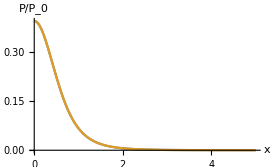

```mathematica
sol1=NDSolve[{1/x D[x ((1+x^2)^3)/2 P'[x],x]==-1/(1+x^2),P[1000]==0,P'[0.001]==0},P,{x,0.0001,1000}]
Plot[{Evaluate[{2P[x]/. sol1}],2PAnalytic[x]},{x,0.0001,5},PlotRange->All,AxesLabel->{"x","P/P_0"}]
```

## (2) Given a Pressure Distribution, get the elastic displacements.

Given a radially symmetric P[r], to get the elastic displacement in z I quote the result from Johnson:

```mathematica
lim=1000;
YM=1;
ν=0.5;
uz[r_,P_]:= 4(1-ν^2)/(π YM)NIntegrate[t/(t+r)P[t]EllipticK[ (4t r)/(t+r)^2],{t,0.001,lim}];
```

InterpolatingFunction[…]

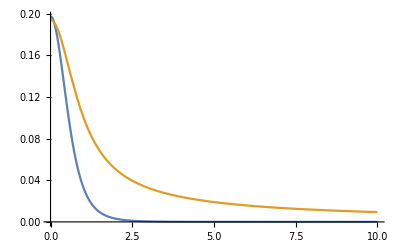

```mathematica
InputP=(P/.sol1)[[1]]
Plot[{PAnalytic[x],uz[x,InputP]},{x,0,10},PlotRange->Full]
```

```mathematica
R=1;
η=1;
h0=0.1;
ρ=1;
Π=1;
```

```mathematica
h[r_]:=h0+r^2/(2 R)
sol1=NDSolve[{1/r D[r (ρ h[r]^3)/(12 η)P'[r],r]==-Π/h[r],P[1]==0,P'[0.001]==0},P,{r,0.001,100}]
sol2=NDSolve[{1/r D[r (ρ h[r]^3)/(12 η)P'[r],r]==-Π/h[r],P[100]==0,P'[0.001]==0},P,{r,0.001,100}]
```

{{P→InterpolatingFunction[…]}}

{{P→InterpolatingFunction[…]}}

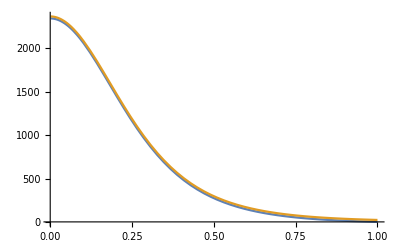

```mathematica
Plot[Evaluate[{{P[r]/. sol1},{P[r]/. sol2}}],{r,0.001,1},PlotRange->All]
```

```mathematica
N[2 π^2-15]/24
```

0.197467

```mathematica
0.2*12
```

2.4

## (3) Putting these together

Below, I express all qunatities nondimensionalised by Hertzian scales. Lets first sketch a few iterations manually

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Simulation parameters*)
```

```mathematica
outercut=10; (* how many Hertzian lengths our simulation goes out to*)
innercut=0.01;
NPoints=50;
grid=Table[r,{r,innercut,outercut,(outercut-innercut)/NPoints}];
(* Material Parameters*)
ϕ=1; (*our dimensionless pressure ratio*)
ν=0.5 (*Poission ratio*)
```

```mathematica
(* initial Guess for h*)
h0=3;
Analytich[r_]:=h0+r^2/2;
h=Interpolation[Table[{r,Analytich[r]},{r,innercut,outercut,(outercut-innercut)/NPoints}]];
```

```mathematica
(* the core simulation loop, without the h0 modifying*)
hlist={};
plist={};
For[i=0,i<10,i++,
Print[i];
(* get the pressure*)
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];
(* from the pressure, get the elastic displacement*)
uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
(* construct an interpolating function over out grid*)
uzovergrid= uz@grid;

(* the new height function*)
hovergrid=h0+grid^2/2+uzovergrid;
h=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];

AppendTo[hlist,h[r]];
AppendTo[plist,Pressure[r]];
]
```

```mathematica
2*π*NIntegrate[r Pressure[r],{r,innercut,outercut}]
```

0.945265

```mathematica
(* the core simulation loop, without the h0 modifying*)
hlist={};
plist={};
(* initial Guess for h*)
h0=3;
For[i=0,i<10,i++,
Analytich[r_]:=h0+r^2/2;
h=Interpolation[Table[{r,Analytich[r]},{r,innercut,outercut,(outercut-innercut)/NPoints}]];
For[j=0,j<6,j++,
Print[" i ",i," j ",j];
(* get the pressure*)
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];
(* from the pressure, get the elastic displacement*)
uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
(* construct an interpolating function over out grid*)
uzovergrid= uz@grid;

(* the new height function*)
hovergrid=h0+grid^2/2+uzovergrid;
h=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];

AppendTo[hlist,h[r]];
AppendTo[plist,Pressure[r]];
];
F=2*π*NIntegrate[r Pressure[r],{r,innercut,outercut}];
(* new h0 guess, depending on whether the force is too big or too small*)
h0=h0 F;
Print[" F ",F];	
Print[" h0 ",h0]
]
```

i 0 j 0

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.409627}. NIntegrate obtained 0.214178 and 6.55501×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.0091}. NIntegrate obtained 0.188032 and 2.15963×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.20882}. NIntegrate obtained 0.177025 and 1.77995×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

i 0 j 1

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

i 0 j 2

i 0 j 3

i 0 j 4

i 0 j 5

F 0.945235

h0 2.8357

i 1 j 0

i 1 j 1

i 1 j 2

i 1 j 3

i 1 j 4

i 1 j 5

F 1.04406

h0 2.96063

i 2 j 0

i 2 j 1

i 2 j 2

i 2 j 3

i 2 j 4

i 2 j 5

F 0.967779

h0 2.86524

i 3 j 0

i 3 j 1

i 3 j 2

i 3 j 3

i 3 j 4

i 3 j 5

F 1.02536

h0 2.93789

i 4 j 0

i 4 j 1

i 4 j 2

i 4 j 3

i 4 j 4

i 4 j 5

F 0.981091

h0 2.88233

i 5 j 0

i 5 j 1

i 5 j 2

i 5 j 3

i 5 j 4

i 5 j 5

F 1.01469

h0 2.92467

i 6 j 0

i 6 j 1

i 6 j 2

i 6 j 3

i 6 j 4

i 6 j 5

F 0.98897

h0 2.89241

i 7 j 0

i 7 j 1

i 7 j 2

i 7 j 3

i 7 j 4

i 7 j 5

F 1.00846

h0 2.91688

i 8 j 0

i 8 j 1

i 8 j 2

i 8 j 3

i 8 j 4

i 8 j 5

F 0.993625

h0 2.89829

i 9 j 0

i 9 j 1

i 9 j 2

i 9 j 3

i 9 j 4

i 9 j 5

F 1.00486

h0 2.91237

```mathematica
Length[hlist]
```

60

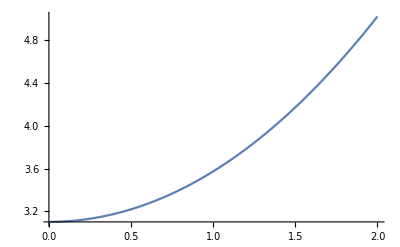

```mathematica
temp=hlist[[{60}]];
Plot[temp,{r,innercut,2}]
```

```mathematica
(* Material Parameters*)
tol=0.01;
ϕ=5; (*our dimensionless pressure ratio*)
(* initial Guess for h*)
(* the core simulation loop, without the h0 modifying*)
hlist={};
plist={};
h0=0.5;
For[i=1,i<4,i++,
Analytich[r_]:=h0+r^2/2;
h=Interpolation[Table[{r,Analytich[r]},{r,innercut,outercut,(outercut-innercut)/NPoints}]];
Newh=h;
err=2tol;
j=0;
While[err>tol,
(* increment iteration counter*)
j++;
Print["j",j];

(* update the current h*)
h=Newh;

(* append to lists*)
AppendTo[hlist,h[r]];
AppendTo[plist,Pressure[r]];

(* ok go! get the pressure*)
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];

(* from the pressure, get the elastic displacement*)
uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
(* construct an interpolating function over out grid*)
uzovergrid= uz@grid;

(* the new height function*)
hovergrid=h0+grid^2/2+uzovergrid;
Newh=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];
err=Abs[((Newh[innercut]-h[innercut])/h[innercut])];
Print[err]
];
F=2*π*NIntegrate[r Pressure[r],{r,innercut,outercut}];
(* new h0 guess, depending on whether the force is too big or too small*)
Print["  previous h0 ",h0];
Print["  F from previous h0 ",F];	
h0=h0 F;
Print[" new h0 ",h0]
]
```

j2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.409616}. NIntegrate obtained 0.667057 and 6.78033×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.20882}. NIntegrate obtained 0.341638 and 4.72915×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.40868}. NIntegrate obtained 0.293476 and 5.02492×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

1.47483

j3

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.469486

j4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.393577

j5

0.190644

j6

0.128358

j7

0.0711664

j8

0.0443189

j9

0.0257597

j10

0.0156082

j11

0.00921337

previous h0 0.5

F from previous h0 0.768977

new h0 0.384488

j12

3.69301

j13

0.72643

j14

1.41332

j15

0.519163

j16

0.717921

j17

0.359031

j18

0.405141

j19

0.241918

j20

0.240474

j21

0.159887

j22

0.146622

j23

0.104221

j24

0.0908128

j25

0.0673238

j26

0.0567803

j27

0.0432134

j28

0.0356947

j29

0.0276217

j30

0.0225061

j31

0.0175954

j32

0.0142231

j33

0.0112075

j34

0.00901623

previous h0 0.384488

F from previous h0 0.947486

new h0 0.364297

j35

4.45887

j36

0.767153

j37

1.81258

j38

0.58921

j39

0.985268

j40

0.444396

j41

0.598253

j42

0.329584

j43

0.383712

j44

0.240919

j45

0.253817

j46

0.174057

j47

0.171047

j48

0.124608

j49

0.11666

j50

0.0886234

j51

0.0801977

j52

0.0627089

j53

0.0554103

j54

0.0442137

j55

0.0384231

j56

0.0310952

j57

0.0267171

j58

0.0218347

j59

0.0185975

j60

0.0152948

j61

0.0129532

j62

0.0107126

j63

0.00904915

previous h0 0.364297

F from previous h0 0.979828

new h0 0.356949

```mathematica
h[innercut]
```

0.25691

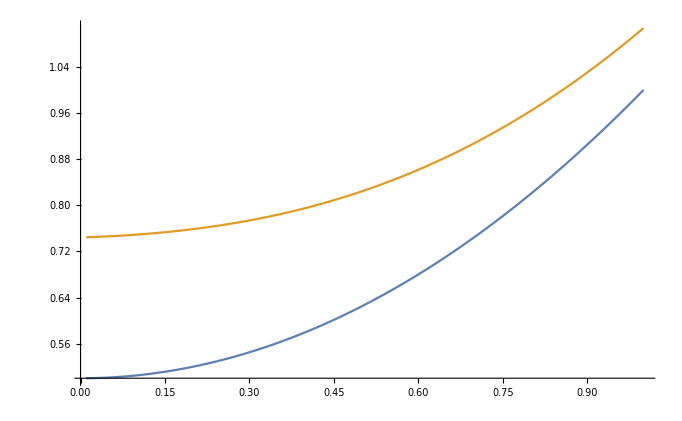

```mathematica
temp=hlist[[{1,62}]];
Plot[temp,{r,innercut,1},PlotRange->All]
```

```mathematica
(* Material Parameters*)
tol=0.01;
ϕ=10; (*our dimensionless pressure ratio*)
(* initial Guess for h*)
(* the core simulation loop, without the h0 modifying*)
hlist={};
plist={};
h0=0.2;
For[i=1,i<4,i++,
Analytich[r_]:=h0+r^2/2;
h=Interpolation[Table[{r,Analytich[r]},{r,innercut,outercut,(outercut-innercut)/NPoints}]];
Newh=h;
err=2tol;
j=0;
While[err>tol,
(* increment iteration counter*)
j++;
Print["j",j];

(* update the current h*)
h=Newh;

(* append to lists*)
AppendTo[hlist,h[r]];
AppendTo[plist,Pressure[r]];

(* ok go! get the pressure*)
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];

(* from the pressure, get the elastic displacement*)
uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
(* construct an interpolating function over out grid*)
uzovergrid= uz@grid;

(* the new height function*)
hovergrid=h0+grid^2/2+uzovergrid;
Newh=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];
err=Abs[((Newh[innercut]-h[innercut])/h[innercut])];
Print[err]
];
F=2*π*NIntegrate[r Pressure[r],{r,innercut,outercut}];
(* new h0 guess, depending on whether the force is too big or too small*)
Print["  previous h0 ",h0];
Print["  F from previous h0 ",F];	
h0=h0 F;
Print[" new h0 ",h0]
]
```

j1

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.209814}. NIntegrate obtained 1.73187 and 7.18736×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.00904}. NIntegrate obtained 0.636836 and 7.25556×10^-7 for the integral and error estimates.

9.04933

j2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.209842}. NIntegrate obtained 0.044892 and 4.84409×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.879089

j3

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

4.51655

j4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.797903

j5

3.04131

j6

0.733605

j7

2.30503

j8

0.680294

j9

1.85946

j10

0.634704

j11

1.55811

j12

0.594827

j13

1.33925

j14

0.559377

j15

1.17219

j16

0.527455

j17

1.03983

j18

0.498419

j19

0.932063

j20

0.471805

j21

0.842359

j22

0.447255

j23

0.766342

j24

0.424472

j25

0.701015

j26

0.40325

j27

0.644157

j28

0.383389

j29

0.594172

j30

0.364756

j31

0.54989

j32

0.34723

j33

0.510326

j34

0.330695

j35

0.474768

j36

0.315075

j37

0.44264

j38

0.300287

j39

0.413428

j40

0.286255

j41

0.386768

j42

0.27294

j43

0.362383

j44

0.260288

j45

0.339916

j46

0.248231

j47

0.319247

j48

0.236783

j49

0.300224

j50

0.225939

j51

0.282548

j52

0.215534

j53

0.266148

j54

0.205636

j55

0.250861

j56

0.196175

j57

0.236623

j58

0.187161

j59

0.22334

j60

0.178553

j61

0.210906

j62

0.170338

j63

0.199301

j64

0.16251

j65

0.188418

j66

0.155033

j67

0.178219

j68

0.147905

j69

0.168659

j70

0.141108

j71

0.15967

j72

0.13461

j73

0.151215

j74

0.128411

j75

0.143259

j76

0.122487

j77

0.135738

j78

0.11682

j79

0.128673

j80

0.111426

j81

0.121987

j82

0.106249

j83

0.115665

j84

0.101306

j85

0.109697

j86

0.0966048

j87

0.104093

j88

0.092125

j89

0.0987908

j90

0.0878444

j91

0.0937436

j92

0.0837314

j93

0.0889741

j94

0.0798222

j95

0.0844738

j96

0.0760891

j97

0.0801981

j98

0.0725163

j99

0.0761455

j100

0.0691047

j101

0.0723071

j102

0.0658759

j103

$Aborted

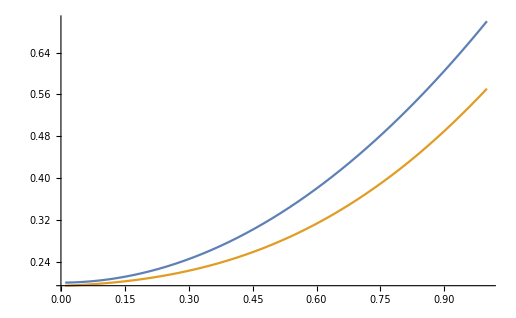

```mathematica
temp=hlist[[{1,103}]];
Plot[{hlist[[1]],hlist[[103]]-0.28},{r,innercut,1},PlotRange->All]
```

```mathematica
(* get the pressure*)
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];
(* from the pressure, get the elastic displacement*)
uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
(* construct an interpolating function over out grid*)
uzovergrid= uz@grid;

(* the new height function*)
hovergrid=h0+grid^2/2+uzovergrid;
h=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.409608}. NIntegrate obtained 3.17529 and 0.0000123353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.50954}. NIntegrate obtained 3.04606 and 3.10658×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.609423}. NIntegrate obtained 2.90375 and 5.5744×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

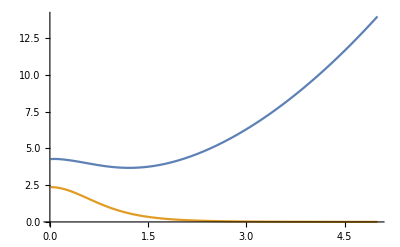

```mathematica
Plot[{h[r],Pressure[r]},{r,innercut,5},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];
(* from the pressure, get the elastic displacement*)
uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
(* construct an interpolating function over out grid*)
uzovergrid= uz@grid;

(* the new height function*)
hovergrid=h0+grid^2/2+uzovergrid;
h=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];
Plot[{h[r],Pressure[r]},{r,innercut,5},PlotRange->All,AxesOrigin->{0,0}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.309705}. NIntegrate obtained 0.303695 and 7.09465×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.509527}. NIntegrate obtained 0.299393 and 6.4953×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.50853}. NIntegrate obtained 0.247359 and 9.93455×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

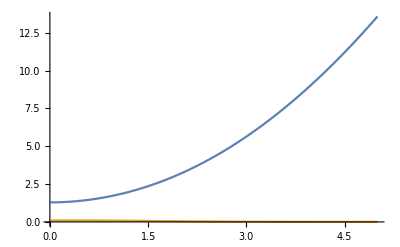

-Graphics-

```mathematica
Plot[{h[r],Pressure[r]},{r,innercut,5},PlotRange->All,AxesOrigin->{0,0}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.309712}. NIntegrate obtained 1.87193 and 3.52269×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.509505}. NIntegrate obtained 1.76705 and 3.55029×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.70931}. NIntegrate obtained 1.63285 and 2.68383×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

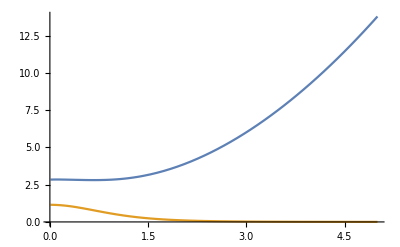

```mathematica
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];
(* from the pressure, get the elastic displacement*)
uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
(* construct an interpolating function over out grid*)
uzovergrid= uz@grid;

(* the new height function*)
hovergrid=h0+grid^2/2+uzovergrid;
h=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];
Plot[{h[r],Pressure[r]},{r,innercut,5},PlotRange->All,AxesOrigin->{0,0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.309727}. NIntegrate obtained 0.519308 and 1.24404×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.909129}. NIntegrate obtained 0.470222 and 3.86953×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.10891}. NIntegrate obtained 0.445456 and 1.37563×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

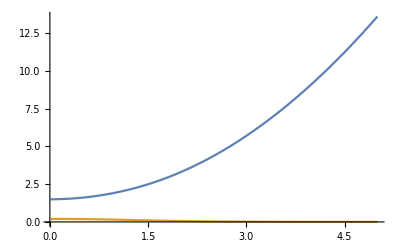

```mathematica
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];
(* from the pressure, get the elastic displacement*)
uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
(* construct an interpolating function over out grid*)
uzovergrid= uz@grid;

(* the new height function*)
hovergrid=h0+grid^2/2+uzovergrid;
h=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];
Plot[{h[r],Pressure[r]},{r,innercut,5},PlotRange->All,AxesOrigin->{0,0}]
```

Below is the core simulation loop:

{}

0

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.309722}. NIntegrate obtained 0.66931 and 5.26325×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.40968}. NIntegrate obtained 0.661276 and 2.19791×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.909112}. NIntegrate obtained 0.593476 and 9.19312×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

1

```mathematica
s=NDSolve[{y'[x]==y[x] Cos[x+y[x]],y[0]==1},y,{x,0,30}]
Plot[Evaluate[y[x]/. s],{x,0,30},PlotRange->All]
```

```mathematica
s
```

```mathematica
y[x]/. s
```

{InterpolatingFunction[…][x]}

```mathematica
hlist[[1]]
```

InterpolatingFunction[…]

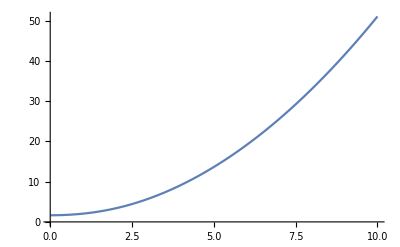

```mathematica
Plot[hlist[[1]][r],{r,innercut,outercut}]
```

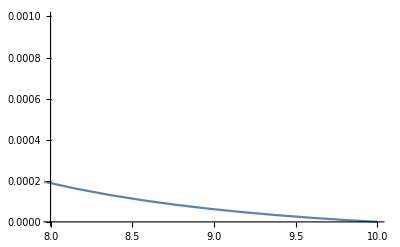

```mathematica
Pressure=NDSolve[{1/r D[r h[r]^3/12 P'[r],r]==1/ϕ^2-1/h[r],P[outercut]==0,P'[innercut]==0},P,{r,innercut,outercut}];
Pressure=(P/.Pressure)[[1]];
Plot[{Pressure[r]},{r,innercut,outercut},PlotRange->{{8,10},{0,0.001}}]
```

```mathematica
(* now with the pressure, get the elastic deformations*)

uz[r_]:=4(1-ν^2)/π NIntegrate[t/(t+r)Pressure[t]EllipticK[ (4t r)/(t+r)^2],{t,innercut,outercut}];
```

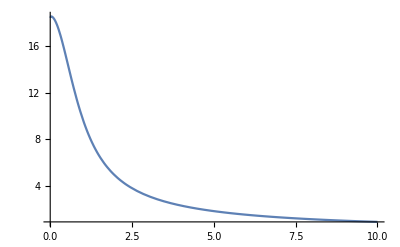

```mathematica
Plot[uz[r],{r,innercut,outercut},PlotRange->All]
```

```mathematica
disp=uz@grid
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.509504}. NIntegrate obtained 15.4854 and 0.00001978 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.709337}. NIntegrate obtained 13.0965 and 0.0000490183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.809254}. NIntegrate obtained 11.9942 and 0.0000214069 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{18.4372,18.3802,17.8135,16.9639,15.9247,14.7875,13.6291,12.5063,11.4536,10.4898,9.62065,8.84478,8.15601,7.54608,7.00622,6.52789,6.10306,5.72488,5.38694,5.08394,4.81128,4.565,4.34175,4.13864,3.95318,3.7834,3.62736,3.48355,3.35064,3.22747,3.11301,3.00641,2.90689,2.81378,2.72648,2.64446,2.56729,2.49452,2.4258,2.36081,2.29924,2.24083,2.18535,2.13256,2.08231,2.03439,1.98865,1.94494,1.90313,1.8631,1.82474,1.78794,1.75261,1.71866,1.68601,1.65459,1.62434,1.59518,1.56706,1.53992,1.51371,1.48839,1.46391,1.44022,1.4173,1.39509,1.37358,1.35273,1.33251,1.31288,1.29383,1.27534,1.25736,1.23989,1.22289,1.20637,1.19028,1.17462,1.15937,1.14451,1.13003,1.11592,1.10215,1.08873,1.07562,1.06284,1.05035,1.03815,1.02624,1.0146,1.00322,0.992093,0.981213,0.97057,0.960156,0.949966,0.93999,0.930223,0.920657,0.911288,0.902109}

```mathematica
(* construct an interpolating function over out grid*)
uzovergrid=disp
hovergrid=h0+grid^2/2+uzovergrid;
h=Interpolation[MapThread[{#1,#2}&,{grid,hovergrid}]];
```

{18.4372,18.3802,17.8135,16.9639,15.9247,14.7875,13.6291,12.5063,11.4536,10.4898,9.62065,8.84478,8.15601,7.54608,7.00622,6.52789,6.10306,5.72488,5.38694,5.08394,4.81128,4.565,4.34175,4.13864,3.95318,3.7834,3.62736,3.48355,3.35064,3.22747,3.11301,3.00641,2.90689,2.81378,2.72648,2.64446,2.56729,2.49452,2.4258,2.36081,2.29924,2.24083,2.18535,2.13256,2.08231,2.03439,1.98865,1.94494,1.90313,1.8631,1.82474,1.78794,1.75261,1.71866,1.68601,1.65459,1.62434,1.59518,1.56706,1.53992,1.51371,1.48839,1.46391,1.44022,1.4173,1.39509,1.37358,1.35273,1.33251,1.31288,1.29383,1.27534,1.25736,1.23989,1.22289,1.20637,1.19028,1.17462,1.15937,1.14451,1.13003,1.11592,1.10215,1.08873,1.07562,1.06284,1.05035,1.03815,1.02624,1.0146,1.00322,0.992093,0.981213,0.97057,0.960156,0.949966,0.93999,0.930223,0.920657,0.911288,0.902109}

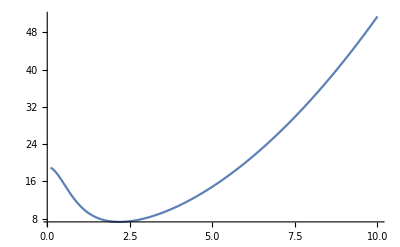

```mathematica
Plot[h[r],{r,0.1,outercut}]
```

```mathematica
disp;
MapThread[{#1,#2}&,{grid,disp}]
dispinterp=Interpolation[MapThread[{#1,#2}&,{grid,disp}]]
Plot[dispinterp[r],{r,innercut,outercut},PlotRange->All]
```

```mathematica
disp+grid
```

{18.4472,18.4901,18.0233,17.2736,16.3343,15.297,14.2385,13.2156,12.2628,11.3989,10.6296,9.95368,9.36481,8.85478,8.41482,8.03639,7.71146,7.43318,7.19514,6.99204,6.81928,6.6729,6.54955,6.44634,6.36078,6.2909,6.23476,6.19085,6.15784,6.13457,6.12001,6.11331,6.11369,6.12048,6.13308,6.15096,6.17369,6.20082,6.232,6.26691,6.30524,6.34673,6.39115,6.43826,6.48791,6.53989,6.59405,6.65024,6.70833,6.7682,6.82974,6.89284,6.95741,7.02336,7.09061,7.15909,7.22874,7.29948,7.37126,7.44402,7.51771,7.59229,7.66771,7.74392,7.8209,7.89859,7.97698,8.05603,8.13571,8.21598,8.29683,8.37824,8.46016,8.54259,8.62549,8.70887,8.79268,8.87692,8.96157,9.04661,9.13203,9.21782,9.30395,9.39043,9.47722,9.56434,9.65175,9.73945,9.82744,9.9157,10.0042,10.093,10.182,10.2713,10.3608,10.4505,10.5404,10.6305,10.7209,10.8114,10.9021}

```mathematica
grid^2/2
```

{0.00005,0.00603901,0.022008,0.047957,0.0838861,0.129795,0.185684,0.251553,0.327402,0.413231,0.50904,0.61483,0.730599,0.856348,0.992077,1.13779,1.29348,1.45914,1.63479,1.82042,2.01603,2.22162,2.43719,2.66274,2.89827,3.14378,3.39927,3.66474,3.94019,4.22562,4.52102,4.82641,5.14178,5.46713,5.80246,6.14777,6.50306,6.86833,7.24358,7.62881,8.02402,8.42921,8.84438,9.26953,9.70466,10.1498,10.6049,11.0699,11.545,12.03,12.525,13.03,13.545,14.0699,14.6049,15.1498,15.7046,16.2695,16.8444,17.4292,18.024,18.6288,19.2436,19.8683,20.503,21.1478,21.8024,22.4671,23.1418,23.8264,24.521,25.2256,25.9402,26.6647,27.3992,28.1438,28.8982,29.6627,30.4372,31.2216,32.016,32.8204,33.6348,34.4591,35.2934,36.1378,36.992,37.8563,38.7306,39.6148,40.509,41.4132,42.3274,43.2515,44.1856,45.1298,46.0838,47.0479,48.022,49.006,50.}

```mathematica
disp
```

{18.4372,18.3802,17.8135,16.9639,15.9247,14.7875,13.6291,12.5063,11.4536,10.4898,9.62065,8.84478,8.15601,7.54608,7.00622,6.52789,6.10306,5.72488,5.38694,5.08394,4.81128,4.565,4.34175,4.13864,3.95318,3.7834,3.62736,3.48355,3.35064,3.22747,3.11301,3.00641,2.90689,2.81378,2.72648,2.64446,2.56729,2.49452,2.4258,2.36081,2.29924,2.24083,2.18535,2.13256,2.08231,2.03439,1.98865,1.94494,1.90313,1.8631,1.82474,1.78794,1.75261,1.71866,1.68601,1.65459,1.62434,1.59518,1.56706,1.53992,1.51371,1.48839,1.46391,1.44022,1.4173,1.39509,1.37358,1.35273,1.33251,1.31288,1.29383,1.27534,1.25736,1.23989,1.22289,1.20637,1.19028,1.17462,1.15937,1.14451,1.13003,1.11592,1.10215,1.08873,1.07562,1.06284,1.05035,1.03815,1.02624,1.0146,1.00322,0.992093,0.981213,0.97057,0.960156,0.949966,0.93999,0.930223,0.920657,0.911288,0.902109}

```mathematica
h[0.1]
```

(0.5+r^2/2+InterpolatingFunction[…])[0.1]

```mathematica
q[r]
```

3+InterpolatingFunction[…][r]

17.8852

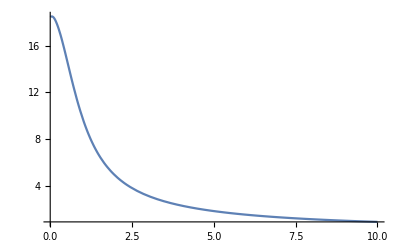

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 0.01.

ReplaceAll::reps: {NDSolve[{(1/12 Power[«2»] ρ Power[«2»] («1»)^(«1»)[«1»]+1/4 r Power[«2»] ρ Power[«2»] InterpolatingFunction[«5»][«1»] («1»)^(«1»)[«1»]+1/12 r Power[«2»] ρ Power[«2»] («1»)^(«1»)[«1»])/r==-1/(InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][r]),P[10]==0,P'[0.01]==0},P,{r,0.01,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand (t EllipticK[(0.04 t)/(0.01+t)^2] P[t])/(0.01+t) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.01,10}}.

NIntegrate::inumr: The integrand (t EllipticK[(0.4396 t)/(0.1099+t)^2] P[t])/(0.1099+t) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.01,10}}.

NIntegrate::inumr: The integrand (t EllipticK[(0.8392 t)/(0.2098+t)^2] P[t])/(0.2098+t) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.01,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
dispinterp[0.2]
Plot[dispinterp[r],{r,innercut,outercut},PlotRange->All]
```

```mathematica
x=2;
For[i=0,i<1,i++,
(* get the pressure*)
Print[x]
]
```

2

```mathematica
a=2
b=a
a=3
b
```

2

2

3

2